## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW170104";

(*键名直接用短名，里面加上下划线*)
inspiralParams={"dphi_0","dphi_2","dphi_3","dphi_4","dphi_5l","dphi_6","dphi_6l","dphi_7"};
intermediateParams={"dbeta_2","dbeta_3"};
mergerParams={"dalpha_2","dalpha_3","dalpha_4"};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

```mathematica
(*绘制中位数比热力图*)
PlotRatioHeatmap[results,"MedianRatios","Median Ratio Heatmap"]

(*绘制宽度比热力图*)
PlotRatioHeatmap[results,"WidthRatios","Width Ratio Heatmap"];

(*绘制下界比热力图*)
PlotRatioHeatmap[results,"LowerBoundRatios","Lower Bound Ratio Heatmap"];

(*绘制上界比热力图*)
PlotRatioHeatmap[results,"UpperBoundRatios","Upper Bound Ratio Heatmap"];
```

Error: ratioType not found in results

## m1-m2 Plot, 22

## INSPIRAL

```mathematica
plots=<||>;
compPlots=<||>;
vsPlots=<||>;
vsPlots["p2p4"]={};
```

### phi_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0001};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 21307 + 镜像 21307

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.49731×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.49731×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.0001}，共 2 条

第一条前3点：{{33.2876,34.2893},{33.1205,34.4188},{32.5709,34.715}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 2 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: True)

区域内总积分值：0.98822

可信水平百分比：98.822%

==========================

dphi_2 预处理完成，红线包含概率 prob = 0.98822

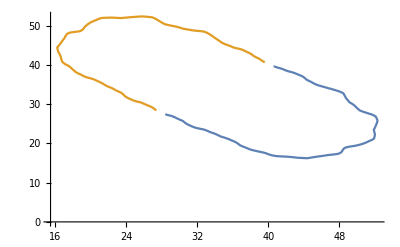

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

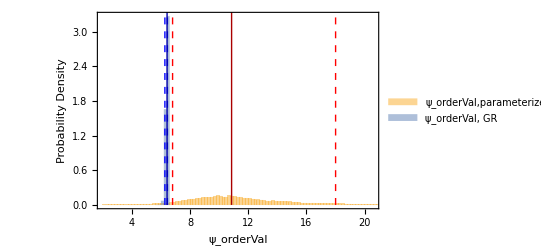

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.03785, 0.96215}

实际使用的 GR 概率区间上下界: {6.25259, 6.44167}

实际使用的 Param 概率区间上下界: {6.43959, 18.7291}

GR下界: 点数=99 | Y>0点数=99 | 平均误差=2.87088×10^-16

GR上界: 点数=99 | Y>0点数=99 | 平均误差=1.33675×10^-15

Param下界: 点数=99 | Y>0点数=99 | 平均误差=8.61264×10^-16

Param上界: 点数=99 | Y>0点数=99 | 平均误差=12.2873

{{2,1.85356},{3,2.78035},{4,3.70713},{5,4.63391},{6,5.56069}}

{{2,1.99983},{3,3.00028},{4,4.00031},{5,4.99982},{6,5.99945}}

chi1L取值：0.459326

chi2L取值：0.4582

=====================================================

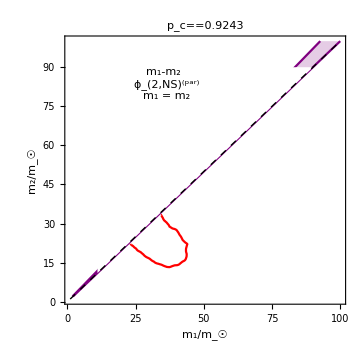

```mathematica
probability=prob;
probability=0.9243;

PlotInversion[p,probability,1,100,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2}]
```

### phi_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.001};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 20224 + 镜像 20224

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.78993×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.78993×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.001}，共 2 条

第一条前3点：{{24.4757,23.4753},{24.4755,23.4738},{24.4957,23.4548}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 2 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: True)

区域内总积分值：0.87778

可信水平百分比：87.778%

==========================

dphi_4 预处理完成，红线包含概率 prob = 0.87778

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

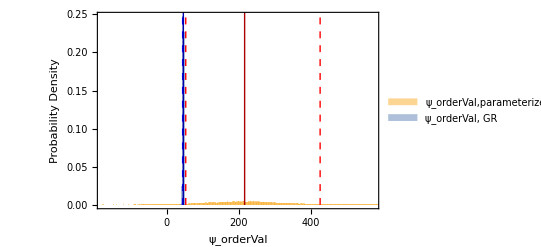

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.0438, 0.9562}

实际使用的 GR 概率区间上下界: {43.8576, 46.244}

实际使用的 Param 概率区间上下界: {46.0001, 438.983}

GR下界: 点数=197 | Y>0点数=197 | 平均误差=4.72493×10^-15

GR上界: 点数=197 | Y>0点数=197 | 平均误差=1.19746×10^-14

Param下界: 点数=197 | Y>0点数=197 | 平均误差=1.98375×10^-15

Param上界: 点数=197 | Y>0点数=197 | 平均误差=392.737

{{4,3.17893},{5,3.97366},{6,4.76839},{7,5.56312},{8,6.35785}}

{{4,4.00129},{5,4.99907},{6,5.99797},{7,6.99984},{8,7.99757}}

chi1L取值：0.509548

chi2L取值：0.467782

=====================================================

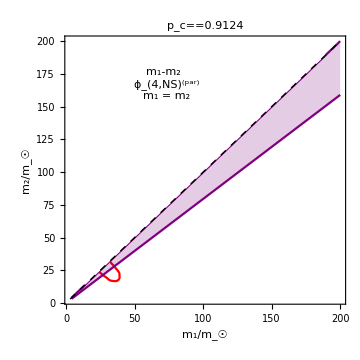

```mathematica
probability=prob;
probability=0.9124;

PlotInversion[p,probability,3,200,1,cm->True,cd->False,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

### phi_5l

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_5l"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.001};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 17541 + 镜像 17541

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.97885×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.97885×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.001}，共 2 条

第一条前3点：{{31.0523,32.0541},{30.977,32.1447},{30.5634,32.5636}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 2 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: True)

区域内总积分值：0.87619

可信水平百分比：87.619%

==========================

dphi_5l 预处理完成，红线包含概率 prob = 0.87619

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

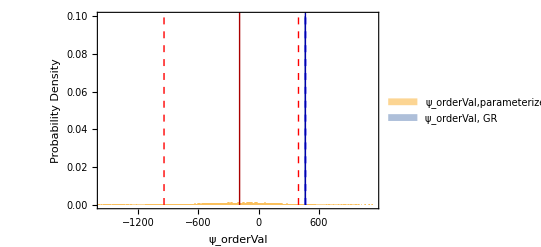

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.0342, 0.9658}

实际使用的 GR 概率区间上下界: {464.758, 466.98}

实际使用的 Param 概率区间上下界: {-1049.02, 465.}

GR下界: 点数=485 | Y>0点数=485 | 平均误差=3.75049×10^-14

GR上界: 点数=485 | Y>0点数=485 | 平均误差=2.61363×10^-14

Param下界: 点数=485 | Y>0点数=485 | 平均误差=1513.77

Param上界: 点数=485 | Y>0点数=485 | 平均误差=2.20341×10^-14

{{3.2,3.19898},{3.4,3.39572},{3.6,3.59615},{3.8,3.79993},{4.,4.00292}}

{{3.2,2.5157},{3.4,2.67293},{3.6,2.83017},{3.8,2.9874},{4.,3.14463}}

chi1L取值：0.418848

chi2L取值：0.455312

=====================================================

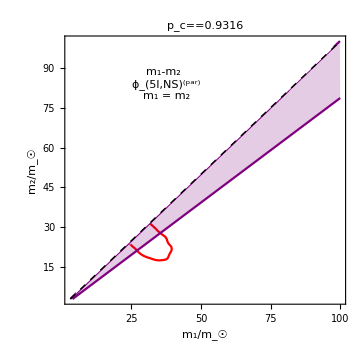

```mathematica
probability=prob;
probability=0.9316;

PlotInversion[p,probability,3,100,0.2,cm->True,cd->True,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiLNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

### phi_6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_6"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.001};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 18248 + 镜像 18248

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.70387×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.70387×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.001}，共 2 条

第一条前3点：{{31.3752,32.377},{31.1085,32.5534},{31.0134,32.6269}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 2 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: True)

区域内总积分值：0.870114

可信水平百分比：87.0114%

==========================

dphi_6 预处理完成，红线包含概率 prob = 0.870114

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

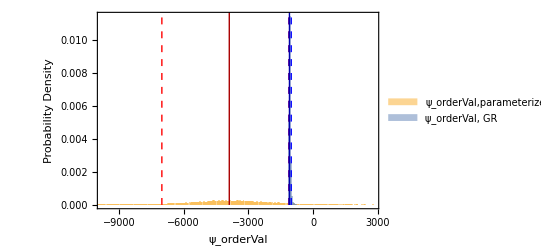

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.04915, 0.95085}

实际使用的 GR 概率区间上下界: {-1103.97, -1006.56}

实际使用的 Param 概率区间上下界: {-7033.68, -1102.5}

GR下界: 点数=970 | Y>0点数=970 | 平均误差=1.08764×10^-13

GR上界: 点数=970 | Y>0点数=970 | 平均误差=1.0642×10^-13

Param下界: 点数=970 | Y>0点数=970 | 平均误差=5929.55

Param上界: 点数=970 | Y>0点数=970 | 平均误差=1.45566×10^-13

{{3.1,3.09995},{3.2,3.20029},{3.3,3.29988},{3.4,3.40012},{3.5,3.49961}}

{{3.1,2.83672},{3.2,2.92823},{3.3,3.01974},{3.4,3.11125},{3.5,3.20275}}

chi1L取值：0.510796

chi2L取值：0.446253

=====================================================

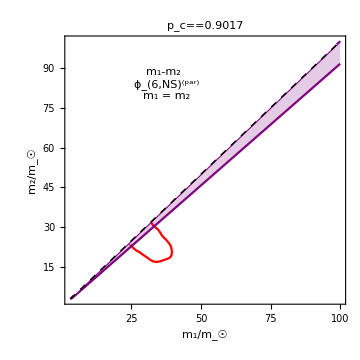

```mathematica
probability=prob;
probability=0.9017;

PlotInversion[p,probability,3,100,0.1,cm->True,cd->True,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

### phi_7

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_7"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0008224};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 17264 + 镜像 17264

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.49368×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.49368×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.0008224}，共 2 条

第一条前3点：{{23.4844,24.1484},{23.2783,24.3426},{23.2757,24.3452}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.905818

可信水平百分比：90.5818%

==========================

dphi_7 预处理完成，红线包含概率 prob = 0.905818

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

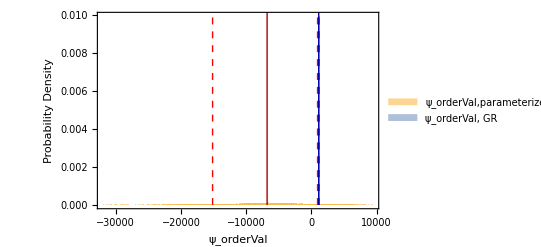

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.0470909, 0.952909}

实际使用的 GR 概率区间上下界: {1112.67, 1130.87}

实际使用的 Param 概率区间上下界: {-15336., 1109.79}

GR下界: 点数=57 | Y>0点数=57 | 平均误差=1.5956×10^-14

GR上界: 点数=57 | Y>0点数=57 | 平均误差=1.07703×10^-13

Param下界: 点数=57 | Y>0点数=57 | 平均误差=16289.7

Param上界: 点数=57 | Y>0点数=57 | 平均误差=1.15681×10^-13

{{4,19293.8},{5,24117.1},{6,28940.3},{7,33763.5},{8,38586.7}}

{{4,1.87203},{5,2.34003},{6,2.80804},{7,3.27605},{8,3.74405}}

chi1L取值：0.479016

chi2L取值：0.448311

=====================================================

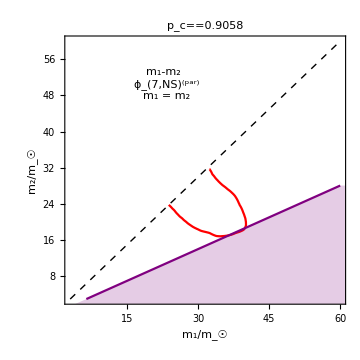

```mathematica
probability=prob;
(*probability=0.903;*)
(*probability=0.9059;*)
PlotInversion[p,probability,3,60,1,cm->True,cd->True,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

## Intermediate

### beta_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.00298};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 20031 + 镜像 20031

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.51317×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.51316×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.00298}，共 2 条

第一条前3点：{{26.3058,25.3041},{26.3514,25.2567},{26.5906,25.0337}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.53572

可信水平百分比：53.572%

==========================

dbeta_2 预处理完成，红线包含概率 prob = 0.53572

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

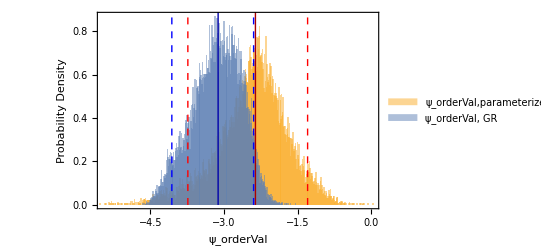

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dbeta_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.23214, 0.76786}

实际使用的 GR 概率区间上下界: {-3.52558, -2.74707}

实际使用的 Param 概率区间上下界: {-2.85468, -1.92801}

GR下界: 点数=50 | Y>0点数=50 | 平均误差=0.213049

GR上界: 点数=50 | Y>0点数=50 | 平均误差=9.05942×10^-16

Param下界: 点数=50 | Y>0点数=50 | 平均误差=8.34888×10^-16

Param上界: 点数=50 | Y>0点数=50 | 平均误差=8.26006×10^-16

{{11,27.1611},{12,29.6303},{13,32.0995},{14,34.5686},{15,37.0378}}

{{11,59.3638},{12,64.7605},{13,70.1572},{14,75.5539},{15,80.9507}}

chi1L取值：0.519556

chi2L取值：0.510708

=====================================================

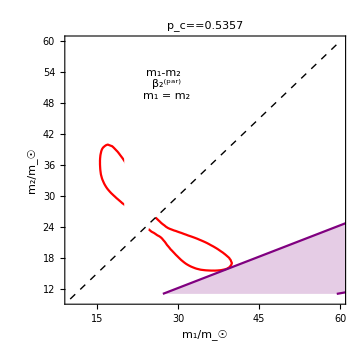

```mathematica
probability=prob;
(*probability=0.401;*)

PlotInversion[p,probability,10,60,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

### beta_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.002};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 20730 + 镜像 20730

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.01287×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.01287×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.002}，共 2 条

第一条前3点：{{22.5627,23.5645},{22.3547,23.7994},{22.2128,23.9581}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.769515

可信水平百分比：76.9515%

==========================

dbeta_3 预处理完成，红线包含概率 prob = 0.769515

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

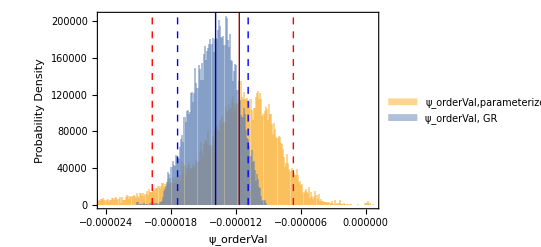

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.46, 0.54}

实际使用的 GR 概率区间上下界: {-0.0000141014, -0.0000136524}

实际使用的 Param 概率区间上下界: {-0.0000120488, -0.0000113477}

GR下界: 点数=57 | Y>0点数=57 | 平均误差=3.53366×10^-7

GR上界: 点数=57 | Y>0点数=57 | 平均误差=1.57518×10^-21

Param下界: 点数=57 | Y>0点数=57 | 平均误差=1.60106×10^-6

Param上界: 点数=57 | Y>0点数=6 | 平均误差=2.42342×10^-7

{{4,39.6929},{5,49.6256},{6,59.5418},{7,69.4745},{8,79.3946}}

{{4,39.6978},{5,49.6187},{6,59.5421},{7,69.4718},{8,79.4096}}

chi1L取值：0.44779

chi2L取值：0.449006

=====================================================

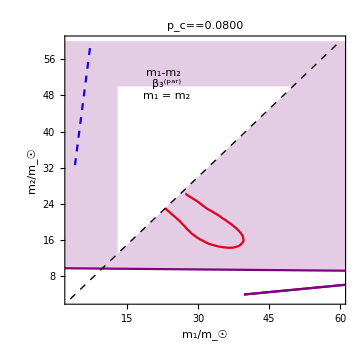

```mathematica
probability=prob;
(*probability=0.11;*)
probability=0.08;
(* 蓝色要对称一下 *)
PlotInversion[p,probability,3,60,1,cm->True,cd->True,cu->True,plotgr->True,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

```mathematica
p="dbeta_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.002};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 20730 + 镜像 20730

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.01287×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.01287×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.002}，共 2 条

第一条前3点：{{22.5627,23.5645},{22.3547,23.7994},{22.2128,23.9581}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.769515

可信水平百分比：76.9515%

==========================

dbeta_3 预处理完成，红线包含概率 prob = 0.769515

```mathematica
probability=prob;
probability=0.3510;

(* 蓝色要对称一下 *)
PlotInversion[p,probability,3,100,1,cm->True,cd->True,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.05,spinPercentile2->0.05,contourIndices->{1},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.3245, 0.6755}

实际使用的 GR 概率区间上下界: {-0.0000148903, -0.0000129341}

实际使用的 Param 概率区间上下界: {-0.0000133728, -0.0000101199}

Greater::nord: Invalid comparison with -1.99718+6.59064 ⅈ attempted.

Greater::nord: Invalid comparison with -2.49647+8.23829 ⅈ attempted.

Greater::nord: Invalid comparison with -2.99576+9.88595 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR下界: 点数=97 | Y>0点数=0 | 平均误差=8.92905×10^-21

GR上界: 点数=97 | Y>0点数=0 | 平均误差=7.23705×10^-21

Param下界: 点数=97 | Y>0点数=3 | 平均误差=1.00602×10^-7

Param上界: 点数=97 | Y>0点数=97 | 平均误差=3.17856×10^-21

{{4,4.},{5,5.},{6,6.},{7,-2.07069+11.2871 ⅈ},{8,-2.3665+12.8995 ⅈ}}

{{4,3.95518},{5,4.94397},{6,5.93276},{7,6.92156},{8,7.91035}}

chi1L取值：0.047747

chi2L取值：0.0482764

=====================================================

-Graphics-

```mathematica
p="dbeta_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.00695};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 20730 + 镜像 20730

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.01287×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.01287×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.00695}，共 2 条

第一条前3点：{{32.6647,18.6807},{32.6696,18.5796},{32.675,18.4682}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.0118056

可信水平百分比：1.18056%

==========================

dbeta_3 预处理完成，红线包含概率 prob = 0.0118056

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.494097, 0.505903}

实际使用的 GR 概率区间上下界: {-0.0000139048, -0.0000138418}

实际使用的 Param 概率区间上下界: {-0.0000117318, -0.0000116277}

Greater::nord: Invalid comparison with 10.1963-4.12748 ⅈ attempted.

Greater::nord: Invalid comparison with 4.23851-11.2265 ⅈ attempted.

Greater::nord: Invalid comparison with 3.6522-12.4764 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR下界: 点数=50 | Y>0点数=0 | 平均误差=1.43927×10^-6

GR上界: 点数=50 | Y>0点数=0 | 平均误差=1.3896×10^-6

Param下界: 点数=50 | Y>0点数=50 | 平均误差=2.20229×10^-21

Param上界: 点数=50 | Y>0点数=50 | 平均误差=2.27005×10^-21

{{11,15.9739},{12,17.4261},{13,18.8783},{14,20.3305},{15,21.7826}}

{{11,17.8406},{12,19.4625},{13,21.0844},{14,22.7062},{15,24.3281}}

chi1L取值：0.047747

chi2L取值：0.449006

=====================================================

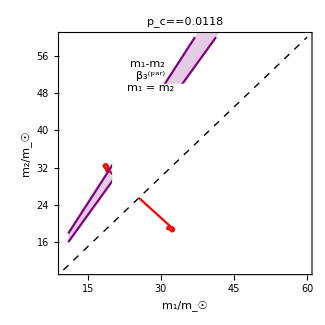

```mathematica
probability=prob;
(*probability=0.01;*)

(* 蓝色要对称一下 *)
PlotInversion[p,probability,10,60,1,cm->True,cd->False,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.05,spinPercentile2->0.5,contourIndices->{1,2}]
```

```mathematica
p="dbeta_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.00442};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 20730 + 镜像 20730

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.48502×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.48502×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.00442}，共 2 条

第一条前3点：{{37.1353,25.0462},{37.1607,25.0337},{37.3242,24.9537}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.171886

可信水平百分比：17.1886%

==========================

```mathematica
p="dbeta_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.00442};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];
```

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.414057, 0.585943}

实际使用的 GR 概率区间上下界: {-0.00001436, -0.000013418}

实际使用的 Param 概率区间上下界: {-0.0000124562, -0.0000109602}

Greater::nord: Invalid comparison with 11.-2.94236×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with 12.-2.84405×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with 13.-3.94632×10^-14 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR下界: 点数=50 | Y>0点数=0 | 平均误差=5.51226×10^-8

GR上界: 点数=50 | Y>0点数=50 | 平均误差=3.04932×10^-21

Param下界: 点数=50 | Y>0点数=50 | 平均误差=2.37169×10^-21

Param上界: 点数=50 | Y>0点数=50 | 平均误差=2.10064×10^-21

{{11,22.6047},{12,24.6596},{13,26.7146},{14,28.7696},{15,30.8245}}

{{11,39.5817},{12,43.18},{13,46.7783},{14,50.3767},{15,53.975}}

chi1L取值：0.047747

chi2L取值：0.931101

=====================================================

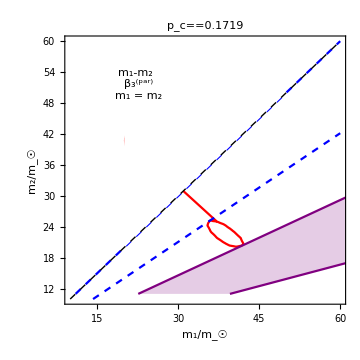

```mathematica
probability=prob;
(*probability=0.1;*)

(* 蓝色要对称一下 *)
PlotInversion[p,probability,10,60,1,cm->True,cd->True,cu->True,plotgr->True,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.05,spinPercentile2->0.95,contourIndices->{1,2}]
```

```mathematica
p="dbeta_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0048};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 20730 + 镜像 20730

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.48502×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.48502×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.0048}，共 2 条

第一条前3点：{{39.2867,20.8679},{39.4595,20.731},{39.5233,20.6986}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.11169

可信水平百分比：11.169%

==========================

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.444155, 0.555845}

实际使用的 GR 概率区间上下界: {-0.0000141889, -0.0000135709}

实际使用的 Param 概率区间上下界: {-0.0000121947, -0.0000112144}

GR下界: 点数=97 | Y>0点数=7 | 平均误差=1.44249×10^-7

GR上界: 点数=97 | Y>0点数=0 | 平均误差=4.36615×10^-21

Param下界: 点数=97 | Y>0点数=97 | 平均误差=4.72605×10^-9

Param上界: 点数=97 | Y>0点数=97 | 平均误差=4.13414×10^-7

{{4,7.96054},{5,9.95068},{6,11.9408},{7,13.9309},{8,15.9211}}

{{4,1.7204×10^6},{5,2.15044×10^6},{6,2.58055×10^6},{7,3.01059×10^6},{8,3.44069×10^6}}

chi1L取值：0.44779

chi2L取值：0.0482764

=====================================================

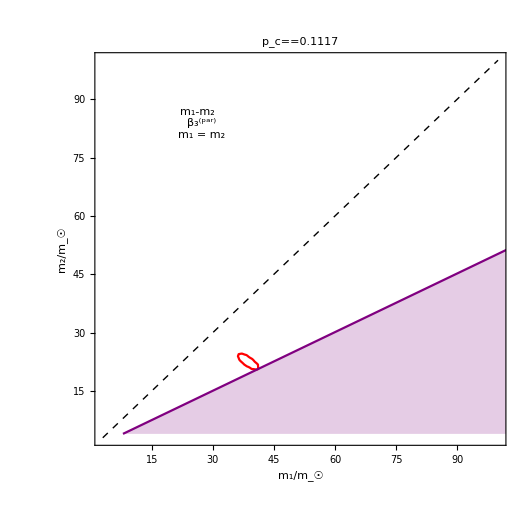

```mathematica
probability=prob;
(*probability=0.1;*)

(* 蓝色要对称一下 *)
PlotInversion[p,probability,3,100,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.05,contourIndices->{1}](*m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]*)
```

```mathematica
p="dbeta_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0027};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 20730 + 镜像 20730

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.48502×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.48502×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.0027}，共 2 条

第一条前3点：{{29.8635,28.8638},{29.8662,28.8645},{29.9017,28.8279}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.557891

可信水平百分比：55.7891%

==========================

dbeta_3 预处理完成，红线包含概率 prob = 0.557891

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.221055, 0.778945}

实际使用的 GR 概率区间上下界: {-0.0000156031, -0.0000123591}

实际使用的 Param 概率区间上下界: {-0.0000147355, -9.18687×10^-6}

GR下界: 点数=97 | Y>0点数=97 | 平均误差=1.6766×10^-21

GR上界: 点数=97 | Y>0点数=97 | 平均误差=2.77687×10^-21

Param下界: 点数=97 | Y>0点数=97 | 平均误差=1.53688×10^-21

Param上界: 点数=97 | Y>0点数=97 | 平均误差=2.63011×10^-6

{{4,9.32292},{5,11.6537},{6,13.9844},{7,16.3151},{8,18.6458}}

{{4,1.98984×10^6},{5,2.48734×10^6},{6,2.98478×10^6},{7,3.48226×10^6},{8,3.97971×10^6}}

chi1L取值：0.44779

chi2L取值：0.931101

=====================================================

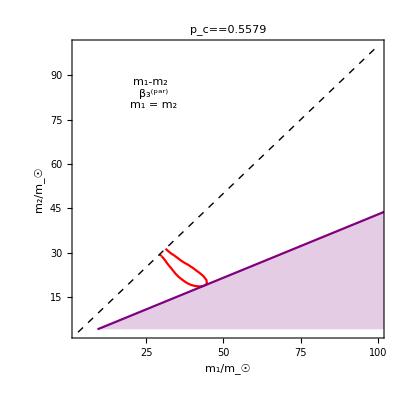

```mathematica
probability=prob;
(*probability=0.6;*)

(* 蓝色要对称一下 *)
PlotInversion[p,probability,3,100,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.95,contourIndices->{1},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.26205, 0.73795}

实际使用的 GR 概率区间上下界: {-0.0000153101, -0.0000125964}

实际使用的 Param 概率区间上下界: {-0.0000141318, -9.59542×10^-6}

GR下界: 点数=50 | Y>0点数=50 | 平均误差=2.84603×10^-21

Greater::nord: Invalid comparison with 11.+4.06554×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with 12.+2.60813×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with 13.+3.32975×10^-14 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR上界: 点数=50 | Y>0点数=0 | 平均误差=1.52302×10^-6

Param下界: 点数=50 | Y>0点数=50 | 平均误差=1.19228×10^-19

Param上界: 点数=50 | Y>0点数=0 | 平均误差=4.52404×10^-6

{{11,10.9402},{12,11.9348},{13,12.9293},{14,13.9239},{15,14.9184}}

{{11,11.+2.35724×10^-14 ⅈ},{12,12.-1.64579×10^-14 ⅈ},{13,13.-1.98858×10^-14 ⅈ},{14,14.+1.92469×10^-14 ⅈ},{15,15.-4.17486×10^-15 ⅈ}}

chi1L取值：0.891411

chi2L取值：0.0482764

=====================================================

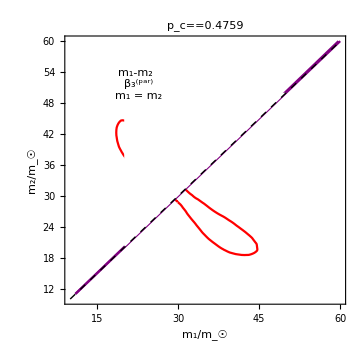

```mathematica
probability=prob;
probability=0.4759;

(* 蓝色要对称一下 *)
PlotInversion[p,probability,10,60,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.95,spinPercentile2->0.05,contourIndices->{1},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.15115, 0.84885}

实际使用的 GR 概率区间上下界: {-0.0000161534, -0.0000118806}

实际使用的 Param 概率区间上下界: {-0.0000160292, -8.45826×10^-6}

GR下界: 点数=32 | Y>0点数=32 | 平均误差=6.14099×10^-21

Greater::nord: Invalid comparison with 19.+1.55373×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with 20.+1.55505×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with 21.+4.30231×10^-14 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR上界: 点数=32 | Y>0点数=0 | 平均误差=4.10496×10^-6

Param下界: 点数=32 | Y>0点数=32 | 平均误差=1.90582×10^-20

Param上界: 点数=32 | Y>0点数=1 | 平均误差=2.35228×10^-7

{{19,18.4964},{20,19.4699},{21,20.4434},{22,21.4169},{23,22.3904}}

{{19,19.},{20,-5.86082},{21,-6.15386},{22,-6.4469},{23,-6.73994}}

chi1L取值：0.891411

chi2L取值：0.449006

=====================================================

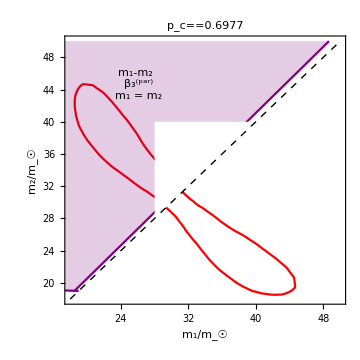

```mathematica
probability=prob;
probability=0.6977;

(* 蓝色要对称一下 *)
PlotInversion[p,probability,18,50,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.95,spinPercentile2->0.5,contourIndices->{1},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.08345, 0.91655}

实际使用的 GR 概率区间上下界: {-0.0000168429, -0.0000112578}

实际使用的 Param 概率区间上下界: {-0.0000180666, -7.47365×10^-6}

GR下界: 点数=350 | Y>0点数=350 | 平均误差=1.22318×10^-6

GR上界: 点数=350 | Y>0点数=350 | 平均误差=6.80832×10^-6

Param下界: 点数=350 | Y>0点数=350 | 平均误差=6.19544×10^-22

Param上界: 点数=350 | Y>0点数=0 | 平均误差=5.85034×10^-20

{{15.1,17.3409},{15.2,17.4558},{15.3,17.5706},{15.4,17.6855},{15.5,17.8003}}

{{15.1,-42.8973},{15.2,-43.1814},{15.3,-43.4655},{15.4,-43.7496},{15.5,-44.0337}}

chi1L取值：0.891411

chi2L取值：0.931101

=====================================================

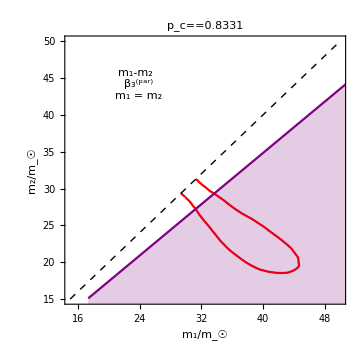

```mathematica
probability=prob;
probability=0.8331;

(* 蓝色要对称一下 *)
PlotInversion[p,probability,15,50,0.1,cm->True,cd->True,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.95,spinPercentile2->0.95,contourIndices->{1},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

# Merger-RingDown

### alpha_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.004875};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
(*prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 22575 + 镜像 22575

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.09148×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.09148×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.004875}，共 2 条

第一条前3点：{{22.0373,27.4158},{22.2895,27.1851},{22.3445,27.1524}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.231196

可信水平百分比：23.1196%

==========================

dalpha_2 预处理完成，红线包含概率 prob = 0.231196

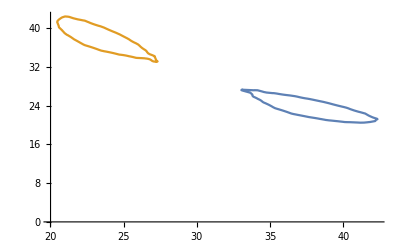

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

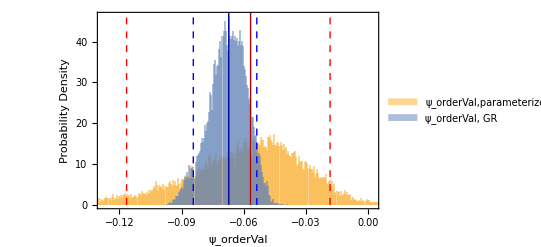

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dalpha_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.384402, 0.615598}

实际使用的 GR 概率区间上下界: {-0.0699778, -0.0644312}

实际使用的 Param 概率区间上下界: {-0.0651947, -0.048737}

GR下界: 点数=40 | Y>0点数=40 | 平均误差=2.74086×10^-17

GR上界: 点数=40 | Y>0点数=40 | 平均误差=1.80411×10^-17

Param下界: 点数=40 | Y>0点数=40 | 平均误差=1.76942×10^-17

Param上界: 点数=40 | Y>0点数=40 | 平均误差=1.07553×10^-17

{{11,22.4875},{12,24.5318},{13,26.5761},{14,28.6204},{15,30.6647}}

{{11,56.4785},{12,61.6129},{13,66.7473},{14,71.8817},{15,77.0161}}

chi1L取值：0.411525

chi2L取值：0.493505

=====================================================

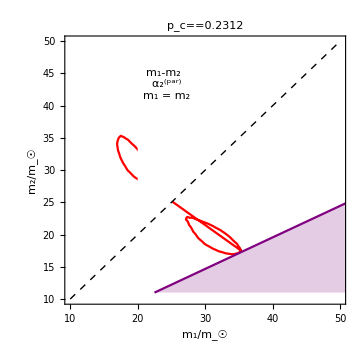

```mathematica
probability=prob;
(*probability=0.2;*)

PlotInversion[p,probability,10,50,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

### alpha_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.005195};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
(*prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.108568

可信水平百分比：10.8568%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.108568

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 19232 + 镜像 19232

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.46018×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.46018×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.005195}，共 2 条

第一条前3点：{{30.4196,18.5869},{30.4314,18.5796},{30.7605,18.39}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.107756

可信水平百分比：10.7756%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.107756

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

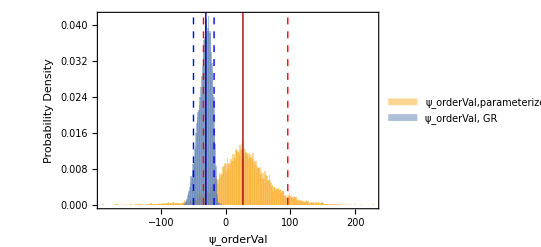

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dalpha_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.446122, 0.553878}

实际使用的 GR 概率区间上下界: {-22.8068, -20.3264}

实际使用的 Param 概率区间上下界: {-19.8161, -9.24899}

GR下界: 点数=40 | Y>0点数=40 | 平均误差=3.05533×10^-14

GR上界: 点数=40 | Y>0点数=40 | 平均误差=2.57572×10^-14

Param下界: 点数=40 | Y>0点数=40 | 平均误差=2.96652×10^-14

Param上界: 点数=40 | Y>0点数=40 | 平均误差=2.39808×10^-14

{{11,20.9872},{12,22.8952},{13,24.8031},{14,26.711},{15,28.619}}

{{11,35.308},{12,38.5178},{13,41.7277},{14,44.9375},{15,48.1473}}

chi1L取值：0.403505

chi2L取值：0.474398

=====================================================

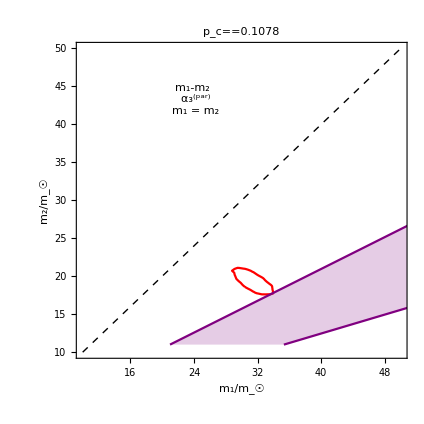

```mathematica
probability=prob;
(*probability=0.2;*)

PlotInversion[p,probability,10,50,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1}]
```

### alpha_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.002};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 20196 + 镜像 20196

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.2535×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.2535×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.002}，共 2 条

第一条前3点：{{22.1432,21.1428},{22.1422,21.1405},{22.3397,20.8051}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

警告：合并后点数不足，无法构成多边形，跳过

Part::partd: Part specification ⟦2⟧ is longer than depth of object.

dalpha_4 预处理完成，红线包含概率 prob = ⟦2⟧

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

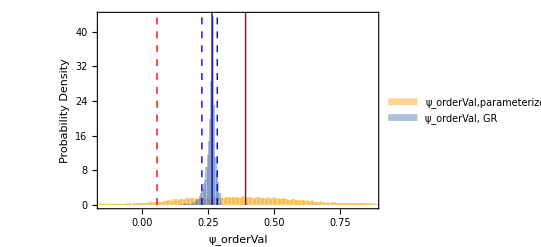

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
probability=prob;
probability=0.3905;

PlotInversion[p,probability,10,50,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2}]
```

====== [dalpha_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.30475, 0.69525}

实际使用的 GR 概率区间上下界: {0.255744, 0.268392}

实际使用的 Param 概率区间上下界: {0.270707, 0.521802}

GR下界: 点数=40 | Y>0点数=40 | 平均误差=1.80411×10^-17

GR上界: 点数=40 | Y>0点数=40 | 平均误差=4.85723×10^-17

Param下界: 点数=40 | Y>0点数=40 | 平均误差=5.96745×10^-17

Greater::nord: Invalid comparison with 0.603554+10.9834 ⅈ attempted.

Greater::nord: Invalid comparison with 0.658423+11.9819 ⅈ attempted.

Greater::nord: Invalid comparison with 0.713291+12.9804 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Param上界: 点数=40 | Y>0点数=0 | 平均误差=0.000127176

{{11,10.6676},{12,11.6374},{13,12.6071},{14,13.5769},{15,14.5467}}

{{11,0.603554+10.9834 ⅈ},{12,0.658423+11.9819 ⅈ},{13,0.713291+12.9804 ⅈ},{14,0.76816+13.9789 ⅈ},{15,0.823029+14.9774 ⅈ}}

chi1L取值：0.475705

chi2L取值：0.4964

=====================================================

-Graphics-

# utils